This tutorial is a semi-systematic compilation of techniques that I’ve accumulated. I wrote it so I wouldn’t forget things I’ve learned, but I also hope it’s useful to anybody who needs to use Mathematica for more than just plotting sin(x).

### Writing functional code

In this example, we will define a probability distribution on 100,000 elements. We ask mathematica to compute the entropy of this probability distribution. There are a variety of ways to code this up. The first way is the “procedural” way and it is probably what you are most familiar with. But Mathematica is optimized to do functional programming and not procedural programming.

```mathematica
p=RandomReal[{0,1},100000];
p=p/Total[p];
```

```mathematica
q=RandomReal[{0,1},100000];
q=q/Total[q];
```

#### For loops/Do loops/While loops are evil! Avoid them if at all possible.

```mathematica
Timing[S=0;
For[i=1,i≤ Length[p],i++,
If[p[[i]]>0,S = S-p[[i]]Log[2,p[[i]]]];
];S]
```

{0.524134,16.3329}

#### Table is less bad but still not great!

```mathematica
Timing[t=Table[If[p[[i]]>0,-p[[i]]*Log[2,p[[i]]],0],{i,1,Length[p]}];Sum[t[[i]],{i,1,Length[p]}]]
```

{0.408731,16.3341}

```mathematica
Total[Table[If[p[[i]]>0,-p[[i]]*Log[2,p[[i]]],0],{i,1,Length[p]}]]//Timing
```

{0.379898,16.3341}

#### Don’t do stupid things!

This code does something very stupid. It tries to use the built in Sum function, but it ends up performing a Table computation over and over and over. This makes the run time horribly long.

```mathematica
Sum[Table[If[p[[i]]>0,-p[[i]]*Log[2,p[[i]]],0],{i,1,Length[p]}][[i]],{i,1,Length[p]}]//Timing
```

$Aborted

#### Linear algebra trick

Convert the sum into the dot product of two vectors. {1,1,1,1,1, etc}.{-p_1log p_1,-p_2log p_2, etc}

```mathematica
hh[p_]:=-p Log[2,p];
```

```mathematica
Timing[pp=Select[p,#>0&];
Dot[ConstantArray[1,Length[pp]],hh/@pp]]
```

{0.242784,16.3329}

#### Functional programming wins! Also the most elegant code.

```mathematica
h[p_List]:=Total[-# Log[2,#]&/@Select[p,#>0&]];
```

```mathematica
h[p]//Timing
```

{0.073878,16.3329}

Q: Why does Mathematica bother with Table if Map is always faster? Can’t it just define 
Table[f[x],{x,1,n}]=f/@Range[n]

Ans: Yes, 99% of the time, Table can be replaced by Map. But Table is slightly more general, since it allows you to run expressions. For example,

```mathematica
f=a;
Table[f=f^2;Cos[x]+f,{x,1,5}]
```

{a^2+Cos[1],a^4+Cos[2],a^8+Cos[3],a^16+Cos[4],a^32+Cos[5]}

You could imagine a situation where you only know how to define f recursively and therefore cannot write down a closed form a function that you can just map onto Range[5]. But in practice, I have found that this is almost never the case. The only exception is that in debugging, it is sometimes helpful to run print commands:

```mathematica
f=a;
Table[f=f^2;Print[f^2];Cos[x]+f,{x,1,5}]
```

a^4

a^8

a^16

a^32

a^64

{a^2+Cos[1],a^4+Cos[2],a^8+Cos[3],a^16+Cos[4],a^32+Cos[5]}

Note that we can sometimes get by Map’s inability to execute expressions by putting expressions in functions:

```mathematica
g[x_]:=(Print[x^2];x^2);
```

```mathematica
g/@Range[5]
```

1

4

9

16

25

{1,4,9,16,25}

#### Compile functions for ultimate performance!

```mathematica
hcomp=Compile[{{p,_Real}},If[p>0,-p Log [2,p],0]];
```

You might also want to play with some options, like turning on parallelization or compiling in C.

```mathematica
Clear[hclazy]
```

```mathematica
hcp=Compile[{{p,_Real}},If[p>0,-p Log [2,p],0],Parallelization->True,CompilationTarget->"C","RuntimeOptions"->"Speed"];
```

```mathematica
h@p//Timing
```

{0.065784,16.3325}

```mathematica
Min@*Eigenvalues@m
```

-25.4875

```mathematica
Total[hcomp/@p]//Timing
```

{0.015347,16.3325}

```mathematica
Total[hcp/@p]//Timing
```

{0.005374,16.3325}

```mathematica
h[p_List]:=Total[hcp/@p];
```

Note that we save a factor of ~35 to ~50 by using this method over the “intro CS” naive method

```mathematica
Timing[
S=0;
For[i=1,i≤ Length[p],i++,
If[p[[i]]>0,S = S-p[[i]]Log[2,p[[i]]]];
];S][[1]]/(h[p]//Timing)[[1]]
```

48.6125

Note that this savings is a linear speed up! If we increase the amount of data by a factor of 10 for example, the savings ratio remainds the same.

```mathematica
p=RandomReal[{0,1},1000000];
p=p/Total[p];
```

```mathematica
Timing[
S=0;
For[i=1,i≤ Length[p],i++,
If[p[[i]]>0,S = S-p[[i]]Log[2,p[[i]]]];
];S][[1]]/(Total[hcomp/@p]//Timing)[[1]]
```

17.954

#### A word of caution

If you need something to evaluate sequentially, do NOT use map. Map will not necessarily evaluate things in sequence, resulting in strange errors.

#### Another word of caution

Always remember to check the complexity of the algorithm you are using. For example, say we want to find the minimum of a list. The second way is vastly superior. In addition to being more optimized, the second line of code has a complexity O(n) instead of O(n log n).

```mathematica
Timing[(First@*Sort)@p]
```

{0.011015,2.71969×10^-10}

```mathematica
Timing[Min@p]
```

{0.000258,2.71969×10^-10}

This might seem obvious in this simple example, but Mathematica can sometimes do funky things.

### Advanced function defining

It is a good idea to restrict your function’s domain to a subset of the real numbers, lists, etc. For example,

```mathematica
Clear[hh];
hh[p_]:=-p Log[2,p];
```

```mathematica
hh[0]
```

Indeterminate

What’s below makes use of Mathematica’s syntax for constraining patterns.

```mathematica
Clear[hh];
hh[p_/;p>0]:=-p Log[2,p];
hh[p_/;p==0]:=0
```

```mathematica
hh[0]
```

0

```mathematica
times=Sort@RandomReal[{0,1},10^3];
Count[times,u_/;0.1<u<0.2]
```

104

Here is a non-trivial example. An example Dirichlet function is 0 if x is irrational and 1 if x is rational.

```mathematica
dirch[p_/;Element[p,Rationals]]:=1
dirch[p_/;!Element[p,Rationals]]:=0
```

```mathematica
dirch/@{1,2/3,π,Sqrt[2],0.77}
```

{1,1,0,0,0}

Here is another useful tip. Mathematica allows you to name a sequence of expressions. This allows you to define functions which can take in arbitrary number of variables:

```mathematica
sciPlot[x__]:=Plot[x,Evaluate@plotsci]
```

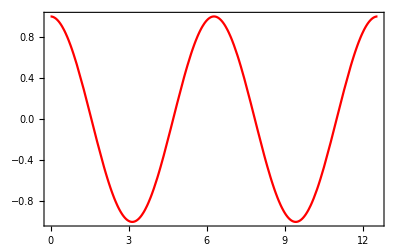

```mathematica
sciPlot[Cos[x],{x,0,4π},PlotStyle->Red]
```

In the above example, it would be terribly cumbersome to define sciPlot by defining its action on one variable, two variables, three variables, ad infinitum.

#### Syntactic sugar

If you want to intimidate people and/or save space

```mathematica
g[x_]:=3x+4;
```

```mathematica
h=3#+4&;
```

The above functions are equivalent

```mathematica
g[z]==h[z]
```

True

Even more scary:

```mathematica
gg[x_,y_,z_]:=3x+4y+5z;
```

```mathematica
hh=3#1+4#2+5#3&;
```

```mathematica
gg[z1,z2,z3]==hh[z1,z2,z3]
```

True

Let’s imagine we have to evaluate the following:

```mathematica
array={3.,2.};
Exp[Tan[Cos[Sin[array[[1]]]]]]
```

4.58997

There are way too many brackets to keep track of. Here is a nicer way to do exactly the same calculation:

```mathematica
Exp@*Tan@*Cos@*Sin@*First@array
```

4.58997

The notation f@x = f[x]. This replaces two characters [,] with a single character. The notation @* means function composition. Once you get used to the notation above, you will never have to keep track of pesky brackets! Putting everything together, we have the standard way of defining a function

```mathematica
f1[x_]:=Exp[Tan[Cos[Sin[x]]]];
```

and the “Advanced” way

```mathematica
f2=Exp@*Tan@*Cos@*Sin;
```

These functions are equivalent.

```mathematica
f1@x==f2@x
```

True

#### Function arguments cannot be redefined

Do not increment or redefine arguments. Instead, redefine the arguments. (This is slightly annoying).

For example, the following code returns an error:

```mathematica
increment[x_]:=Module[{},x++;x];
increment[3]
```

But this code runs fine:

```mathematica
increment[x_]:=Module[{y=x},y++;y];
increment[3]
```

4

### Advanced saving and loading

In our previous example, we generated a large dataset p randomly. The next time we quit the kernel and re-start mathematica, p will be different. How can we avoid this? More generally, if we have some raw data and then we perform some complicated operation on it, how do we avoid re-doing this complicated operation every time?

DumpSave and Get (abbreviated <<) come to the rescue! These are extremely efficient operations to use on huge datasets. Check out the wolfram tutorials if you don’t believe me. (You should almost never use any other methods for saving/loading data. Most of the other methods will take forever to save/load)

```mathematica
?DumpSave
```

DumpSave[file.mx,symbol] writes definitions associated with a symbol to a file in internal Wolfram System format. 
DumpSave[file.mx,context`] writes out definitions associated with all symbols in the specified context. 
DumpSave[file.mx,{object_1,object_2,…}] writes out definitions for several symbols or contexts. 
DumpSave[package`,objects] chooses the name of the output file based on the computer system used.

```mathematica
h[p]
```

19.6528

```mathematica
DumpSave["random.mx",p];
```

```mathematica
p={0.5,0.54,0.1};h[p]
```

1.31224

Now I load p again, et voilà, we are back in business.

```mathematica
<<random.mx
```

```mathematica
h[p]
```

19.6528

If you are forgetful like me, you might want to recall what definitions are contained in the file random.mx. Simply restart the kernel and run

```mathematica
Names["Global`*"]
```

{bias,disk,errorsci,fp,gen,k,l,labelsci,line,makeErrorbars,minf,mInfoFunc,n,plotsci,w,x}

```mathematica
<<random.mx;Complement[Names["Global`*"],n]
```

{p}

In the previous example, note that I have by default two variables labelsci, plotsci. These are custom variables that I load every time mathematica opens. They can be found in the init.m file which is probably somewhere in /user/Library/Mathematica.

See this link for more info:
http://mathematica.stackexchange.com/questions/16401/user-defined-functions-how-to-save-them-for-future-use

This is also a good point to introduce these extras which I have pre-defined:

```mathematica
(**User Mathematica initialization file**)plotsci={Frame->True,FrameStyle->Thickness[.002],LabelStyle->Directive[FontSize->14,Black]};
labelsci={RotateLabel->True,LabelStyle->Directive[FontSize->14,FontFamily->"Helvetica"]};
```

These extras are super useful for making publication-quality plots easily:

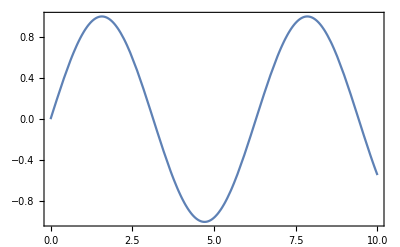
-Graphics-Sin(x)x

```mathematica
Labeled[Plot[Sin[x],{x,0,10},Evaluate[plotsci]],{"Sin(x)","x"},{Left,Bottom},labelsci]
```

Finally, one thing that irritates me about Mathematica is that once you execute a line of code, it jumps to the next line, like a out of control monkey.
To civilize Mathematica, put this in the init.m

```mathematica
SetOptions[EvaluationNotebook[],CellEpilog:>(SelectionMove[EvaluationNotebook[],All,EvaluationCell];
SelectionMove[EvaluationNotebook[],After,CellContents];)]
```

Say you want to export a series of variables, but don’t want to go through the hassle of exporting them individually. Here is a useful script:

```mathematica
SetAttributes[export,HoldAll]
export[var_]:=Export["~/code/mathematica/"<>SymbolName@Unevaluated@var<>".dat",var]
Map[export ,Unevaluated@{var1,var2,var3,var4}]
```

Notice our use of both HoldAll and Unevaluated

### Advanced debugging & Misc tools

Reap and sow is a slightly better form of Print, because you can save the output. This makes it useful for deubgging.

```mathematica
var=Reap[Sow[a];b;Sow[c];7*7]
```

{49,{{a,c}}}

It is also highly useful if you are doing everything in a functional style. You can define a function with sow inside of it for example:

```mathematica
fsow:=Cos[Sow[#+2π Range[-3,3]];#]&
```

```mathematica
Reap[fsow[0]]
```

{1,{{{-6 π,-4 π,-2 π,0,2 π,4 π,6 π}}}}

Also check out Mathematica’s Debugger (Evaluation → Debugger), which can sometimes be very useful when you have a long code and don’t know where in some long function is the problem. The Show Breakpoints option is very useful

One thing that is annoying about mathematica is that one often needs to quit the Kernel.
One can do this by editing MenuSetup.tr, located in /Applications/Mathematica.app/Contents/SystemFiles/FrontEnd/TextResources/Macintosh/

I inserted the following code which makes

Menu["Quit Local",
 	{
    		MenuItem["Quit Kernel",
       	FrontEnd`KernelExecute[ToExpression["Quit[]"]],
       	MenuKey["q", Modifiers -> {"Control"}],
       	MenuEvaluator -> Automatic]
  	}],

Another thing that is highly useful is to start more than one kernel: https://support.wolfram.com/12425?src=mathematica

### Help with full Simplify

One weird thing about Mathematica is that FullSimplify is not as good as it gets. Here is an example:

Here is an example of a function which is clear just -x for x<0.

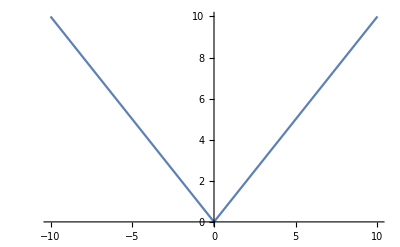

```mathematica
Plot[ArcCosh@*Cosh@x,{x,-10,10}]
```

Nevertheless, full simplify does not simplify it.

```mathematica
FullSimplify[ArcCosh@*Cosh@x,Assumptions->{x<0}]
```

ArcCosh[Cosh[x]]

Here is a workaround. If we put in explicitly a negative real number, e.g., -γ, mathematica can simplify it.

```mathematica
ArcCosh@*Cosh@-EulerGamma
```

EulerGamma

It is important to put in a constant which is unrelated to the problem. To generate a list of positive real constants which are pretty independent, I use this command. This is pretty safe, as long as you don’t expect Stieltjes to show up in your problem:

```mathematica
constgen=Abs@*StieltjesGamma@#&;
```

```mathematica
constgen@4
```

StieltjesGamma[4]

```mathematica
ArcCosh@*Cosh@(-constgen@4)
```

StieltjesGamma[4]